## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\Algebra"];
<<Algebra`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
(* Algebra Package Test *)
G3=DirectProduct[Z[3],U[3]]
CayleyTable[G3,Mode->Visual]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

Groupoid[{{0,1},{0,2},{1,1},{1,2},{2,1},{2,2}},-Operation-]

"Group properties""Element properties""Group Calculator"

* | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,1} | {0,1} | {0,2} | {1,1} | {1,2} | {2,1} | {2,2}
{0,2} | {0,2} | {0,1} | {1,2} | {1,1} | {2,2} | {2,1}
{1,1} | {1,1} | {1,2} | {2,1} | {2,2} | {0,1} | {0,2}
{1,2} | {1,2} | {1,1} | {2,2} | {2,1} | {0,2} | {0,1}
{2,1} | {2,1} | {2,2} | {0,1} | {0,2} | {1,1} | {1,2}
{2,2} | {2,2} | {2,1} | {0,2} | {0,1} | {1,2} | {1,1}  Z[3] x U[3]

## Topic-1

### Definition / Theorem

This is text.

#### Example

## Topic-2

### Exercise 1.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

Complex Analysis

Exercises Ahlfors

## 1.1.1 Arithmetic Operations

### Exercise 1.A.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.C

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.D

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.A

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.C

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.D

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.A

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

## 1.1.2 Square Roots

### Exercise 1.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 4.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

## TEMP

```mathematica
Integrate[1/(√(t^5+t)),{t,0,x},Assumptions->{x in Reals && x>0}]
```

2 √x Hypergeometric2F1[1/8,1/2,9/8,-x^4]

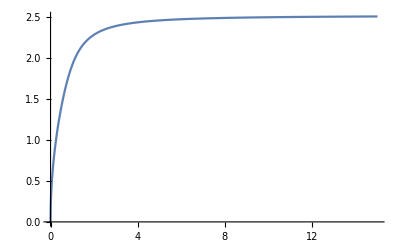

```mathematica
Plot[2 √x Hypergeometric2F1[1/8,1/2,9/8,-x^4],{x,0,15},AxesOrigin->{0,0}]
```

```mathematica
u[x_,y_]:=x/(1+√(x^2+y^2))+I y/(1+√(x^2+y^2))
```

```mathematica
u[0,0]
u[1,0]
u[-1/10,0]
u[0,1]
u[0,10000]
u[4,40000]//N
```

0

1/2

-1/11

ⅈ/2

(10000 ⅈ)/10001

0.0000999975+0.999975 ⅈ

```mathematica
f[n_]:=1/6 n(n+1)(2n+1)
```

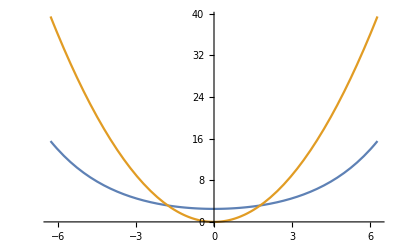

```mathematica
Plot[{1/(.4)Cosh[.4x],x^2},{x,-2π,2π},AxesOrigin->{0,0}]
```

```mathematica
g[x_]:=1/(.4)Cosh[.4x]
g[4]
```

6.44366